# When should genomic imprinting affect sexual maturation?

```mathematica
Clear["Global`*"]
```

## Parameters

```mathematica
tdip={tff->1/2,tmf->1/2,tfm->1/2,tmm->1/2};
thapdip={tff->1/2,tmf->1,tfm->1/2,tmm->0};
```

Fecundity and survival functions:

```mathematica
ϕ[a_]:=(k a)^3
σ[a_]:=Exp[-μ a]
```

## Fitness expressions a_f

```mathematica
wff=1/2 tff f[afi](((1-df)s[afji])/(f[afff](1-df)s[afjff]+f[af]df s[af])+(df s[afji])/(f[af]s[af]));
```

```mathematica
wmf=1/2 tmf f[afi]((nm(1-dm))/(nf(f[afff](1-dm)+f[af]dm))+(nm dm)/(nf f[af]));
wfm=1/2 tfm nf/nm(l f[affm](((1-df)s[afji])/(f[affm](1-df)s[afjfm]+f[af]df s[af])+(df s[afji])/(f[af]s[af]))+(1-l)s[afji]/s[af]);
wmm=1/2 tmm nf/nm(l f[affm]((nm(1-dm))/(nf(f[affm](1-dm)+f[af]dm))+(nm dm)/(nf f[af]))+(1-l)nm/nf);
```

## Fitness expressions a_m

```mathematica
wamff=1/2 tff ;
```

```mathematica
wammf=1/2 tmf ((nm(1-dm)s[amji])/(nf((1-dm)s[amjmf]+dm s[am]))+(nm dm s[amji])/(nf s[am]));
wamfm=1/2 tfm nf/nm(l f[ami]/f[ammm]+(1-l)f[ami]/f[am]);
wammm=1/2 tmm nf/nm(l f[ami]/f[ammm]((nm(1-dm)s[amji])/(nf((1-dm)s[amjmm]+dm s[am]))+(nm dm s[amji])/(nf s[am]))+(1-l)(nm f[ami]s[amji])/(nf f[am]s[am]));
```

## Reproductive values, class frequencies

Demographical model of homogeneous population

```mathematica
A={{wff,wfm},{wmf,wmm}}/.{affm->af,afff->af,afjfm->af,afjff->af,afji->af,afi->af}//Simplify
```

{{tff/2,(nf tfm)/(2 nm)},{(nm tmf)/(2 nf),tmm/2}}

```mathematica
evals=Simplify[Eigenvalues[A]]
```

{1/4 (tff+tmm-√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)),1/4 (tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2))}

```mathematica
classfreqs=Simplify[Eigenvectors[1/evals[[2]] A]]
```

{{-(nf (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1},{(nf (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nm tmf),1}}

```mathematica
repvals=Simplify[Eigenvectors[1/evals[[2]] Transpose[A]]]
```

{{-(nm (-tff+tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1},{(nm (tff-tmm+√(tff^2+4 tfm tmf-2 tff tmm+tmm^2)))/(2 nf tfm),1}}

### Diplodiploidy

Stable class frequencies

```mathematica
udipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.tdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
udip={uf->udipR[[1]],um->udipR[[2]]};
```

Individual reproductive values

```mathematica
vdipR=Simplify[repvals[[2]]/Total[udipR.repvals[[2]]]/.tdip]
```

{(nf+nm)/(2 nf),(nf+nm)/(2 nm)}

```mathematica
vdip={vf->vdipR[[1]],vm->vdipR[[2]]};
```

Class reproductive values

```mathematica
cdip={cf->vf uf,cm->vm um}/.vdip/.udip
```

{cf→1/2,cm→1/2}

### Haplodiploidy

```mathematica
uhapdipR=Simplify[classfreqs[[2]]/Total[classfreqs[[2]]]/.thapdip]
```

{nf/(nf+nm),nm/(nf+nm)}

```mathematica
uhapdip={uf->uhapdipR[[1]],um->uhapdipR[[2]]};
```

Individual reproductive values

```mathematica
vhapdipR=Simplify[repvals[[2]]/Total[uhapdipR.repvals[[2]]]/.thapdip]
```

{(2 (nf+nm))/(3 nf),(nf+nm)/(3 nm)}

```mathematica
vhapdip={vf->vhapdipR[[1]],vm->vhapdipR[[2]]};
```

Class reproductive values

```mathematica
chapdip={cf->vf uf,cm->vm um}/.vhapdip/.uhapdip
```

{cf→2/3,cm→1/3}

## Selection gradient on a_f

```mathematica
Wfaf=wff+vm/vf wmf;
Wmaf=wmm+vf/vm wfm;
```

```mathematica
selgradaf=cf(D[Wfaf,afi]rfi+D[Wfaf,afji]rfkidf+D[Wfaf,afff]rff+D[Wfaf,afjff]rflocjf)+cm(D[Wmaf,afji]rmkidf+D[Wmaf,affm]rmf+D[Wmaf,afjfm]rmlocjf)/.{afi->af,afji->af,afff->af,afjff->af,affm->af,afjfm->af}//Simplify
```

1/(2 nf nm vf vm f[af] s[af])(-(cf nm vm (nf ((-1+df)^2 rff-rfi) tff vf+nm ((-1+dm)^2 rff-rfi) tmf vm)+cm l nf rmf vf (-2 df nf tfm vf+df^2 nf tfm vf+(-2+dm) dm nm tmm vm)) s[af] f'[af]+nf vf (cm nf (rmkidf-(-1+df)^2 l rmlocjf) tfm vf+cf nm (rfkidf-(-1+df)^2 rflocjf) tff vm) f[af] s'[af])

## Selection gradient on a_m

```mathematica
Wfam=wamff+vm/vf wammf;
Wmam=wammm+vf/vm wamfm;
```

```mathematica
selgradam=cf(D[Wfam,amji]rfkidm+D[Wfam,amjmf]rflocjm)+cm(D[Wmam,ami]rmi+D[Wmam,amji]rmkidm+D[Wmam,ammm]rmm+D[Wmam,amjmm]rmlocjm)/.{amji->am,amjmf->am,ami->am,ammm->am,amjmm->am}//Simplify
```

(cm nf (rmi-l rmm) vf (nf tfm vf+nm tmm vm) s[am] f'[am]-nm vm (cm nf (-rmkidm+(-1+dm)^2 l rmlocjm) tmm vf+cf nm (-rfkidm+(-1+dm)^2 rflocjm) tmf vm) f[am] s'[am])/(2 nf nm vf vm f[am] s[am])

## Relatedness

### Diplodiploidy

#### Coefficients of consanguinity

```mathematica
hf=1-df;
hm=1-dm;
```

```mathematica
Qdip={QffJ==QmmJ==QfmJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
Qf==1/2(1+l Qfm),
Qf==Qm,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsoldip=Solve[Qdip,{QffJ,QmmJ,QfmJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients

```mathematica
rdip={
rfi->Qf,
rmi->Qm,
rfkidm->Qm,
rfkidf->Qf,
rmkidf->Qf,
rmkidm->Qm,
rff->1/nf Qf+(nf-1)/nf Qff,
rmf->Qmf,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmlocjf->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf
}/.Qsoldip;
```

Expression by mother (M)

```mathematica
rdipM={
rfi->1/2(Qf+l Qfm),
rmi->1/2(Qf+l Qfm),
rfkidm->1/2(Qf+l Qfm),
rfkidf->1/2(Qf+l Qfm),
rmkidf->l Qfm,
rmkidm->l Qfm,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmm->1/2(1/nm Qf+(nm-1)/nm Qff)+1/2 l Qfm,
rflocjf->Qff,
rflocjm->Qff,
rmlocjf->Qfm,
rmlocjm->Qfm
}/.Qsoldip;
```

Expression by father (P)

```mathematica
rdipP={
rfi->1/2(Qm+l Qfm),
rmi->1/2(Qm+l Qfm),
rfkidf->l Qfm,
rfkidm->l Qfm,
rmkidm->1/2(Qm+l Qfm),
rmkidf->1/2(Qm+l Qfm),
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf l (l Qmm +Qfm),
rmf->1/2 l 1/nm(Qm+ Qfm)+1/2(nm-1)/nm l (l Qmm +Qfm),
rmm->1/2 1/nm(Qm+l Qfm)+1/2(nm-1)/nm l (l Qmm +Qfm),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l Qmm,
rmlocjm->l Qmm
}/.Qsoldip;
```

Expression by maternally-inherited alleles (MI)

```mathematica
rdipMI={
rfi->Qf,
rmi->Qm,
rfkidf->1,
rfkidm->1,
rmkidf->Qfm,
rmkidm->Qfm,
rff->1/2 1/nf(1+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rfm->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmf->1/2 1/nf(Qf+l Qfm)+1/2(nf-1)/nf(Qff+l Qfm),
rmm->1/2 1/nm(1+l Qfm)+1/2(nm-1)/nm(Qff+l Qfm),
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsoldip;
```

```mathematica
rdipPI={
rfi->Qf,
rmi->Qm,
rfkidf->l Qfm,
rfkidm->l Qfm,
rmkidf->1,
rmkidm->1,
rff->1/2 1/nf(1+l Qfm)+1/2(nf-1)/nf l(l Qmm+Qfm),
rfm->1/2 l 1/nm(Qm+l Qfm)+1/2(nm-1)/nm l (l Qmm+Qfm),
rmf->1/2 l 1/nm(Qm+l Qfm)+1/2(nm-1)/nm l (l Qmm+Qfm),
rmm->1/2 1/nm(1+l Qfm)+1/2(nm-1)/nm l (l Qmm+Qfm),
rflocjf->l Qfm,
rflocjm->l Qfm,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->l(1/nm Qm+(nm-1)/nm Qmm)}/.Qsoldip;
```

### Haplodiploidy

#### Coefficients of consanguinity haplodiploidy

```mathematica
Qhapdip={QffJ==1/4(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm+1/4 l^2(1/nm Qm+(nm-1)/nm Qmm),
QfmJ==QmfJ==1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
QmmJ==1/nf Qf+(nf-1)/nf Qff,
Qf==1/2(1+l Qfm),
Qm==1,
Qff==hf^2 QffJ,
Qmm==hm^2 QmmJ,
Qfm==hf hm QfmJ,
Qmf==Qfm};
```

```mathematica
Qsolhapdip=Solve[Qhapdip,{QffJ,QmmJ,QfmJ,QmfJ,Qff,Qf,Qm,Qmm,Qfm,Qmf}]//Simplify//Flatten;
```

#### Relatedness coefficients haplodiploidy

Expression of alleles in offspring

```mathematica
rhapdip={
rfi->Qf,
rmi->Qm,
rfkidf->Qf,
rfkidm->Qm,
rmkidf->Qf,
rmkidm->Qfm,
rff->1/nf Qf+(nf-1)/nf Qff,
rfm->Qmf,
rmf->Qmf,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->1/2 l(1/nm Qm+(nm-1)/nm Qmm)+1/2 Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by mother (M)

```mathematica
rhapdipM={
rfi->1/2(Qf+l Qfm),
rmi->Qf,
rfkidf->1/2(Qf+l Qfm),
rfkidm->Qf,
rmkidf->1/2(Qf+l Qfm),
rmkidm->Qfm,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rfm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmf->1/nf Qf+(nf-1)/nf Qff,
rmm->1/nm Qf+(nm-1)/nm Qff,
rflocjf->Qff,
rflocjm->Qff,
rmlocjf->Qmf,
rmlocjm->Qmf
}/.Qsolhapdip;
```

Expression controlled by father (P)

```mathematica
rhapdipP={
rfi->1/2(Qm+l Qfm),
rmi->Qm,
rfkidf->l Qfm,
rfkidm->Qm,
rmkidf->1/2(Qm+l Qfm),
rmkidm->Qfm,
rff->1/2 1/nf(Qm+l Qfm)+1/2(nf-1)/nf l(l Qmm+Qfm),
rfm->1/2 l 1/nm(Qm+ Qfm)+1/2(nm-1)/nm l(l Qmm+Qfm),
rmf->l Qmf,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l Qmm,
rmlocjm->Qmf
}/.Qsolhapdip;
```

```mathematica
rhapdipMI={
rfi->Qf,
rmi->Qm,
rfkidf->1,
rfkidm->1,
rmkidf->Qfm,
rmkidm->Qfm,
rff->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rfm->1/2(1/nf Qf+(nf-1)/nf Qff)+1/2 l Qfm,
rmf->1/nf Qf+(nf-1)/nf Qff,
rmm->1/nm+(nm-1)/nm Qmm,
rflocjf->1/nf Qf+(nf-1)/nf Qff,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->Qmf,
rmlocjm->Qmf}/.Qsolhapdip;
```

```mathematica
rhapdipPI={
rfi->Qf,
rmi->Qm,
rfkidf->l Qfm,
rfkidm->Qm,
rmkidf->1,
rmkidm->Qfm,
rff->1/2 1/nf(1+Qfm)+1/2(nf-1)/nf l(Qfm+l Qmm),
rmf->Qmf,
rfm->Qfm,
rmm->1/nm Qm+(nm-1)/nm Qmm,
rflocjf->l Qfm,
rflocjm->1/nf Qf+(nf-1)/nf Qff,
rmlocjf->l(1/nm Qm+(nm-1)/nm Qmm),
rmlocjm->Qmf}/.Qsolhapdip;
```

## Analytical results diplodiploidy

```mathematica
afamsol=Solve[{selgradaf==0,selgradam==0},{s'[af],s'[am]}]/.vdip/.cdip/.{tff->1/2,tfm->1/2,tmf->1/2,tmm->1/2}//FullSimplify//Flatten
```

{s'[af]→(((2+(-2+df) df+(-2+dm) dm) rff-2 rfi+((-2+df) df+(-2+dm) dm) l rmf) s[af] f'[af])/((rfkidf-(-1+df)^2 rflocjf+rmkidf-(-1+df)^2 l rmlocjf) f[af]),s'[am]→-(2 (rmi-l rmm) s[am] f'[am])/((rfkidm-(-1+dm)^2 rflocjm+rmkidm-(-1+dm)^2 l rmlocjm) f[am])}

```mathematica
rfcoeff={rfselfjuvf->rfkidf+rmkidf,
rfcompetingjuvf->hf^2(rflocjf+l rmlocjf),
rfownoffspring->rfi+l rmf,
rfcompetingoffspring->1/2(hf^2+hm^2)(rff+l rmf)
};
rmcoeff={rmselfjuvm->rmkidm+rfkidm,
rmcompetingjuvm->hm^2(rflocjm+l rmlocjm),
rmownoffspring->rmi,
rmcompetingoffspring->l rmm};
```

Check algebra s’[af]

```mathematica
(((rfownoffspring-rfcompetingoffspring)s[af])/(-1/2(rfselfjuvf-rfcompetingjuvf))f'[af]/f[af]/.rfcoeff)==(s'[af]/.afamsol)//Simplify
```

True

Check algebra s’[am]

```mathematica
(((rmownoffspring-rmcompetingoffspring)s[am])/(-1/2(rmselfjuvm-rmcompetingjuvm))f'[am]/f[am]/.rmcoeff)==(s'[am]/.afamsol)//Simplify
```

True

```mathematica
rmselfjuvm
```

rmselfjuvm

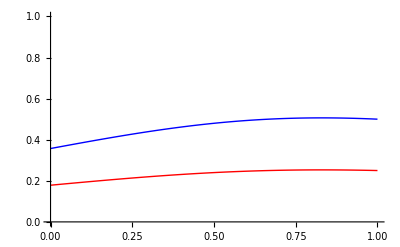

```mathematica
Plot[{.5(rmselfjuvm-rmcompetingjuvm)/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rmownoffspring-rmcompetingoffspring/.rmcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm}},
{dm,0,1},PlotStyle->{Blue,Red},PlotRange->{{0,1},{0,1}}]
```

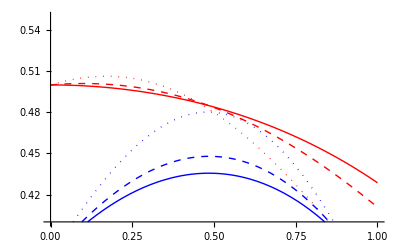

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->1,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->1-dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->1-dm}
},
{dm,0,1},PlotStyle->{{Red,Dotted},{Red,Dashed},{Red},{Blue,Dotted},{Blue,Dashed},{Blue}},PlotRange->{{0,1},{0.4,.55}}]
```

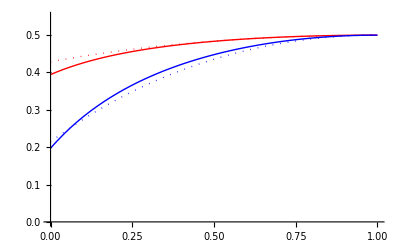

```mathematica
Plot[{.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5(rfselfjuvf-rfcompetingjuvf)/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfownoffspring-rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

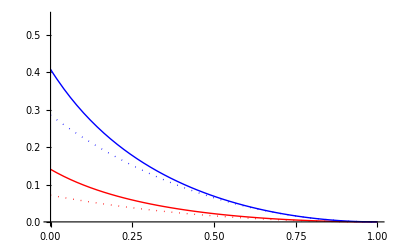

```mathematica
Plot[{.5rfcompetingjuvf/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
.5 rfcompetingjuvf/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0.5,nm->2,nf->2,df->dm},
rfcompetingoffspring/.rfcoeff/.rdip/.{l->0,nm->2,nf->2,df->dm}
},
{dm,0,1},PlotStyle->{{Red},{Red,Dotted},{Blue},{Blue,Dotted}},PlotRange->{{0,1},{0,.55}}]
```

## Results diplodiploidy

```mathematica
ans[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdip/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipMI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipPI/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansM[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipM/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ansP[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rdipP/.vdip/.cdip/.tdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{2,2},{0.9,0.1,1},{1,1/3}]
```

{af→2.43706,am→1.5}

```mathematica
a1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{dm,dm,1},{1,1/3}],{dm,0.01,1,0.01}];
a2=Table[{{dm,af},{dm,am}}/.ans[{2,2},{dm,dm,.8},{1,1/3}],{dm,0.01,1,0.01}];
a3=Table[{{dm,af},{dm,am}}/.ans[{2,2},{dm,dm,.5},{1,1/3}],{dm,0.01,1,0.01}];
```

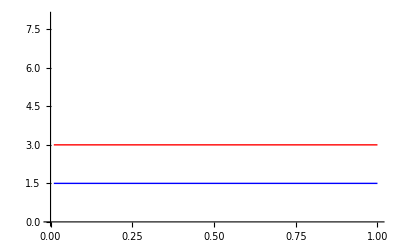

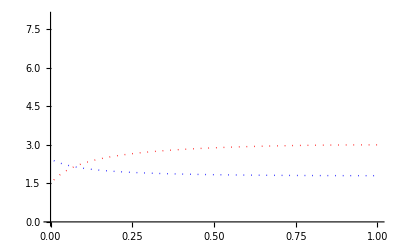

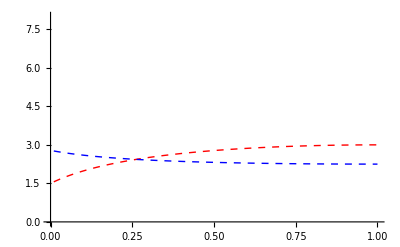

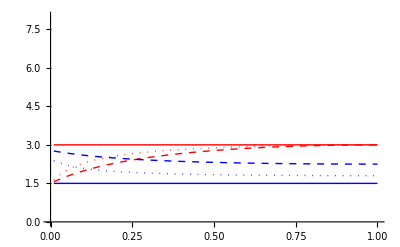

```mathematica
p1=ListLinePlot[Transpose[a1],PlotRange->{0,8},PlotStyle->{Red,Blue}]
p2=ListLinePlot[Transpose[a2],PlotRange->{0,8},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
p3=ListLinePlot[Transpose[a3],PlotRange->{0,8},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
Show[p1,p2,p3]
```

So result from Johnstone & Kuijper recovered: when sex-differences in dispersal are absent, once there is some nonlocal mating increasing philopatry accelerates female lifespan, yet slows down male life span.

Now check some imprinting results with individual-based sims (in which fem-biased dispersal was held constant) without nonlocal male mating. Things change:

```mathematica
a1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{.5,dm,.5},{1,1/3}],{dm,0,1,0.01}];
a1m=Table[{{dm,af},{dm,am}}/.ansM[{2,2},{.5,dm,.5},{1,1/3}],{dm,0.01,1,0.01}];
a1p=Table[{{dm,af},{dm,am}}/.ansP[{2,2},{.5,dm,.5},{1,1/3}],{dm,0.01,1,0.01}];
a2=Table[{{dm,af},{dm,am}}/.ansMI[{2,2},{.5,dm,.5},{1,1/3}],{dm,0,1,0.01}];
a3=Table[{{dm,af},{dm,am}}/.ansPI[{2,2},{.5,dm,.5},{1,1/3}],{dm,0,1,0.01}];
```

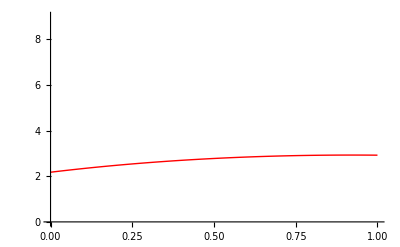

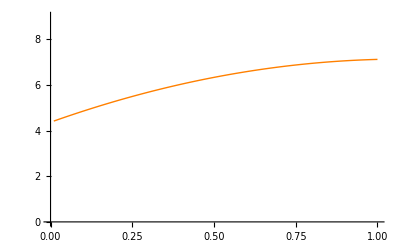

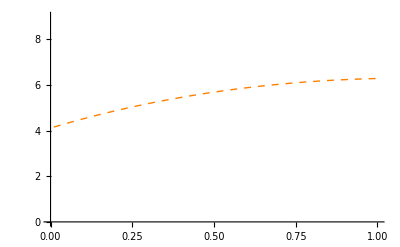

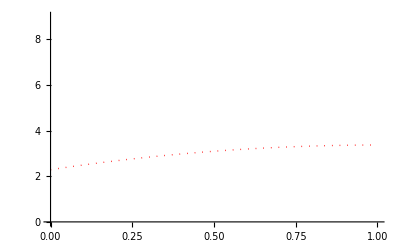

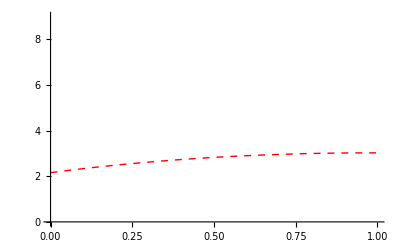

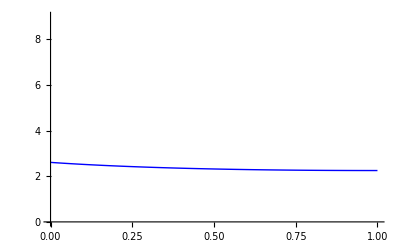

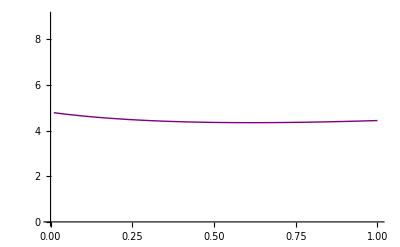

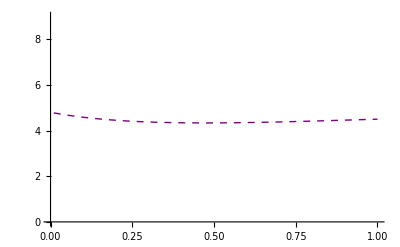

```mathematica
p1=ListLinePlot[Transpose[a1][[1]],PlotRange->{0,9},PlotStyle->{Red}]
p1m=ListLinePlot[Transpose[a1m][[1]],PlotRange->{0,9},PlotStyle->{{Orange}}]
p1p=ListLinePlot[Transpose[a1p][[1]],PlotRange->{0,9},PlotStyle->{{Orange,Dashed}}]
p2=ListLinePlot[Transpose[a2][[1]],PlotRange->{0,9},PlotStyle->{{Red,Dotted}}]
p3=ListLinePlot[Transpose[a3][[1]],PlotRange->{0,9},PlotStyle->{{Red,Dashed}}]
(* same for am *)
p1am=ListLinePlot[Transpose[a1][[2]],PlotRange->{0,9},PlotStyle->{Blue}]
p1mam=ListLinePlot[Transpose[a1m][[2]],PlotRange->{0,9},PlotStyle->{{Purple}}]
p1pam=ListLinePlot[Transpose[a1p][[2]],PlotRange->{0,9},PlotStyle->{{Purple,Dashed}}]
p2am=ListLinePlot[Transpose[a2][[2]],PlotRange->{0,9},PlotStyle->{{Blue,Dotted}}]
p3am=ListLinePlot[Transpose[a3][[2]],PlotRange->{0,9},PlotStyle->{{Blue,Dashed}}]
z1=Show[p1,p1m,p1p,p2,p3]
z2=Show[p1am,p1mam,p1pam,p2am,p3am]
GraphicsGrid[{{z1,z2}},ImageSize->{1000,250}]
```

```mathematica
a1MI=Table[{{dm,af},{dm,am}}/.ansMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,2.625},{0.,2.}},{{0.05,2.74032},{0.05,1.93897}},{{0.1,2.85066},{0.1,1.8799}},{{0.15,2.95617},{0.15,1.82302}},{{0.2,3.05695},{0.2,1.76856}},{{0.25,3.15306},{0.25,1.71669}},{{0.3,3.24453},{0.3,1.66755}},{{0.35,3.33133},{0.35,1.62125}},{{0.4,3.41337},{0.4,1.57786}},{{0.45,3.4905},{0.45,1.53744}},{{0.5,3.5625},{0.5,1.5}},{{0.55,3.62906},{0.55,1.46556}},{{0.6,3.68976},{0.6,1.43411}},{{0.65,3.7441},{0.65,1.40562}},{{0.7,3.79142},{0.7,1.38007}},{{0.75,3.83094},{0.75,1.3574}},{{0.8,3.86165},{0.8,1.33758}},{{0.85,3.88238},{0.85,1.32055}},{{0.9,3.89166},{0.9,1.30627}},{{0.95,3.88773},{0.95,1.29467}},{{1.,3.86842},{1.,1.28571}}}

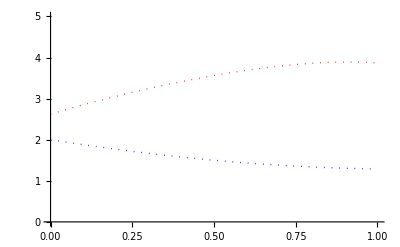

```mathematica
p1MI=ListLinePlot[Transpose[a1MI],PlotRange->{0,5},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
```

```mathematica
a1PI=Table[{{dm,af},{dm,am}}/.ansPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,2.625},{0.,1.89474}},{{0.05,2.75935},{0.05,1.8241}},{{0.1,2.88411},{0.1,1.7626}},{{0.15,2.99963},{0.15,1.70917}},{{0.2,3.10619},{0.2,1.6629}},{{0.25,3.20397},{0.25,1.62302}},{{0.3,3.2931},{0.3,1.5889}},{{0.35,3.37361},{0.35,1.55999}},{{0.4,3.44545},{0.4,1.5358}},{{0.45,3.50848},{0.45,1.51593}},{{0.5,3.5625},{0.5,1.5}},{{0.55,3.6072},{0.55,1.4877}},{{0.6,3.64218},{0.6,1.47874}},{{0.65,3.66698},{0.65,1.47285}},{{0.7,3.68104},{0.7,1.46981}},{{0.75,3.68373},{0.75,1.46939}},{{0.8,3.67434},{0.8,1.47139}},{{0.85,3.65212},{0.85,1.47563}},{{0.9,3.61623},{0.9,1.48192}},{{0.95,3.56581},{0.95,1.4901}},{{1.,3.5},{1.,1.5}}}

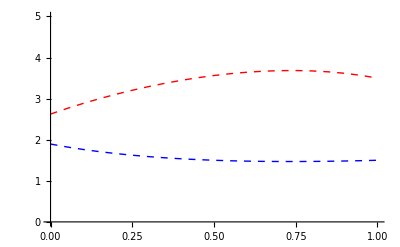

```mathematica
p1PI=ListLinePlot[Transpose[a1PI],PlotRange->{0,5},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
```

```mathematica
a1P=Table[{{dm,af},{dm,am}}/.ansP[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,6.},{0.,5.}},{{0.05,6.20242},{0.05,4.06861}},{{0.1,6.3834},{0.1,3.51035}},{{0.15,6.54544},{0.15,3.14633}},{{0.2,6.6901},{0.2,2.897}},{{0.25,6.81818},{0.25,2.72165}},{{0.3,6.92989},{0.3,2.5974}},{{0.35,7.0249},{0.35,2.51046}},{{0.4,7.10243},{0.4,2.45209}},{{0.45,7.16131},{0.45,2.41655}},{{0.5,7.2},{0.5,2.4}},{{0.55,7.21664},{0.55,2.39984}},{{0.6,7.2091},{0.6,2.41433}},{{0.65,7.17504},{0.65,2.44233}},{{0.7,7.11197},{0.7,2.48319}},{{0.75,7.01739},{0.75,2.53659}},{{0.8,6.88889},{0.8,2.60252}},{{0.85,6.7243},{0.85,2.68125}},{{0.9,6.52189},{0.9,2.77325}},{{0.95,6.28055},{0.95,2.8792}},{{1.,6.},{1.,3.}}}

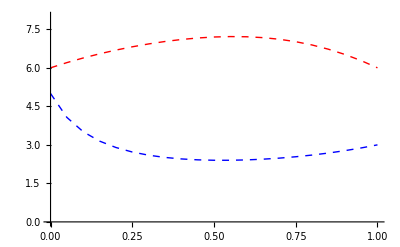

```mathematica
p1P=ListLinePlot[Transpose[a1P],PlotRange->{0,8},PlotStyle->{{Red,Dashed,Thick},{Blue,Dashed,Thick}}]
```

```mathematica
a1M=Table[{{dm,af},{dm,am}}/.ansM[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,6.},{0.,3.}},{{0.05,6.1233},{0.05,2.95314}},{{0.1,6.23817},{0.1,2.89937}},{{0.15,6.34756},{0.15,2.84039}},{{0.2,6.45426},{0.2,2.77778}},{{0.25,6.56098},{0.25,2.71304}},{{0.3,6.67046},{0.3,2.64755}},{{0.35,6.78562},{0.35,2.5825}},{{0.4,6.90966},{0.4,2.51896}},{{0.45,7.04629},{0.45,2.45786}},{{0.5,7.2},{0.5,2.4}},{{0.55,7.37641},{0.55,2.34608}},{{0.6,7.58286},{0.6,2.29673}},{{0.65,7.82933},{0.65,2.25252}},{{0.7,8.12987},{0.7,2.21402}},{{0.75,8.50515},{0.75,2.18182}},{{0.8,8.98712},{0.8,2.15655}},{{0.85,9.62808},{0.85,2.13897}},{{0.9,10.5203},{0.9,2.12998}},{{0.95,11.8432},{0.95,2.13077}},{{1.,14.},{1.,2.14286}}}

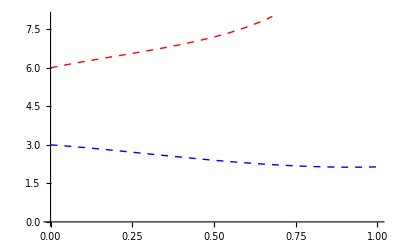

```mathematica
p1M=ListLinePlot[Transpose[a1M],PlotRange->{0,8},PlotStyle->{{Red,Dashed,Thick},{Blue,Dashed,Thick}}]
```

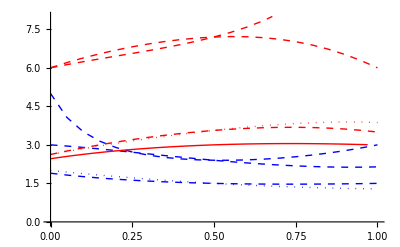

```mathematica
Show[{p1P,p1M,p1,p1MI,p1PI}]
```

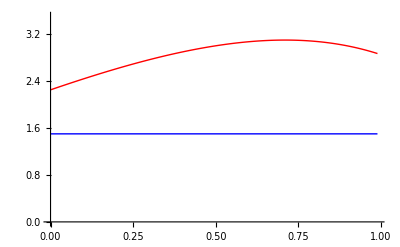

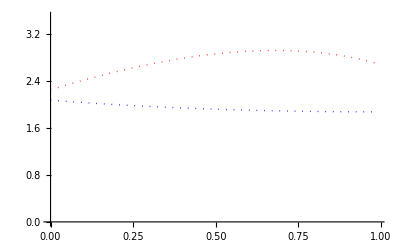

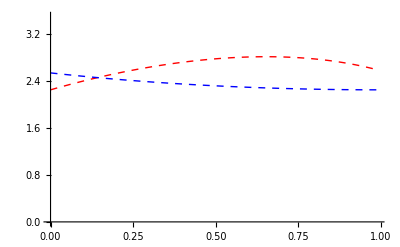

```mathematica
basetabl1=Table[{{dm,af},{dm,am}}/.ans[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,.99,0.01}];
basetabl2=Table[{{dm,af},{dm,am}}/.ans[{2,2},{1-dm,dm,.75},{1,1/3}],{dm,0,.99,0.01}];
basetabl3=Table[{{dm,af},{dm,am}}/.ans[{2,2},{1-dm,dm,.5},{1,1/3}],{dm,0,.99,0.01}];


p1=ListLinePlot[Transpose[basetabl1],PlotRange->{0,3.5},PlotStyle->{{Red},{Blue}}]
p2=ListLinePlot[Transpose[basetabl2],PlotRange->{0,3.5},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
p3=ListLinePlot[Transpose[basetabl3],PlotRange->{0,3.5},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
```

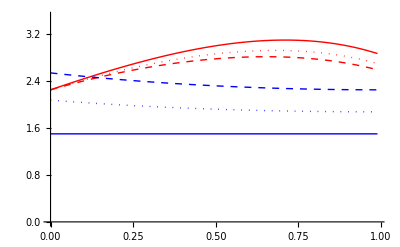

```mathematica
Show[p1,p2,p3]
```

## Results haplodiploidy

```mathematica
anshap[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdip/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapMI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipMI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
anshapPI[{nfs_,nms_},{dfs_,dms_,ls_},{μs_,ks_}]:=
FindRoot[{selgradaf,selgradam}/.rhapdipPI/.vhapdip/.chapdip/.thapdip/.{f->ϕ,s->σ}/.{nf->nfs,nm->nms,df->dfs,dm->dms,μ->μs,k->ks,l->ls},{{af,1.5},{am,1.5}}]
```

```mathematica
ans[{4,4},{0.9,0.1,0.5},{1,1/3}]
```

{af→2.70062,am→2.73356}

```mathematica
a1h=Table[{{dm,af},{dm,am}}/.anshap[{2,2},{1-dm,dm,1},{1,0.3333}],{dm,0,1,0.05}]
```

{{{0.,2.25},{0.,1.5}},{{0.05,2.34128},{0.05,1.5}},{{0.1,2.42803},{0.1,1.5}},{{0.15,2.51075},{0.15,1.5}},{{0.2,2.58984},{0.2,1.5}},{{0.25,2.66561},{0.25,1.5}},{{0.3,2.73829},{0.3,1.5}},{{0.35,2.80802},{0.35,1.5}},{{0.4,2.87488},{0.4,1.5}},{{0.45,2.9389},{0.45,1.5}},{{0.5,3.},{0.5,1.5}},{{0.55,3.05806},{0.55,1.5}},{{0.6,3.11287},{0.6,1.5}},{{0.65,3.16413},{0.65,1.5}},{{0.7,3.21147},{0.7,1.5}},{{0.75,3.25441},{0.75,1.5}},{{0.8,3.29232},{0.8,1.5}},{{0.85,3.32444},{0.85,1.5}},{{0.9,3.34981},{0.9,1.5}},{{0.95,3.3672},{0.95,1.5}},{{1.,3.375},{1.,1.5}}}

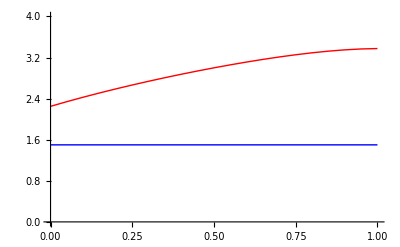

```mathematica
p1h=ListLinePlot[Transpose[a1h],PlotRange->{0,4},PlotStyle->{Red,Blue}]
```

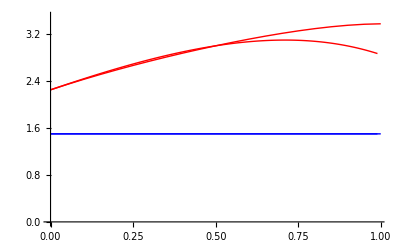

```mathematica
Show[p1,p1h]
```

```mathematica
a1MIh=Table[{{dm,af},{dm,am}}/.anshapMI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,3.375},{0.,1.5}},{{0.05,3.40311},{0.05,1.5}},{{0.1,3.43136},{0.1,1.5}},{{0.15,3.45997},{0.15,1.5}},{{0.2,3.48911},{0.2,1.5}},{{0.25,3.51889},{0.25,1.5}},{{0.3,3.54939},{0.3,1.5}},{{0.35,3.58061},{0.35,1.5}},{{0.4,3.61248},{0.4,1.5}},{{0.45,3.64483},{0.45,1.5}},{{0.5,3.67742},{0.5,1.5}},{{0.55,3.70986},{0.55,1.5}},{{0.6,3.74164},{0.6,1.5}},{{0.65,3.77208},{0.65,1.5}},{{0.7,3.80029},{0.7,1.5}},{{0.75,3.82514},{0.75,1.5}},{{0.8,3.84519},{0.8,1.5}},{{0.85,3.85865},{0.85,1.5}},{{0.9,3.86323},{0.9,1.5}},{{0.95,3.85603},{0.95,1.5}},{{1.,3.83333},{1.,1.5}}}

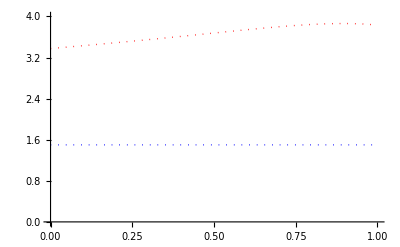

```mathematica
p1MIh=ListLinePlot[Transpose[a1MIh],PlotRange->{0,4},PlotStyle->{{Red,Dotted},{Blue,Dotted}}]
```

```mathematica
a1PIh=Table[{{dm,af},{dm,am}}/.anshapPI[{2,2},{1-dm,dm,1},{1,1/3}],{dm,0,1,0.05}]
```

{{{0.,2.0625},{0.,1.5}},{{0.05,2.18539},{0.05,1.5}},{{0.1,2.30177},{0.1,1.5}},{{0.15,2.4127},{0.15,1.5}},{{0.2,2.5191},{0.2,1.5}},{{0.25,2.62174},{0.25,1.5}},{{0.3,2.72135},{0.3,1.5}},{{0.35,2.81861},{0.35,1.5}},{{0.4,2.91421},{0.4,1.5}},{{0.45,3.00887},{0.45,1.5}},{{0.5,3.10345},{0.5,1.5}},{{0.55,3.19893},{0.55,1.5}},{{0.6,3.29653},{0.6,1.5}},{{0.65,3.3978},{0.65,1.5}},{{0.7,3.50475},{0.7,1.5}},{{0.75,3.61997},{0.75,1.5}},{{0.8,3.74696},{0.8,1.5}},{{0.85,3.89044},{0.85,1.5}},{{0.9,4.05693},{0.9,1.5}},{{0.95,4.25563},{0.95,1.5}},{{1.,4.5},{1.,1.5}}}

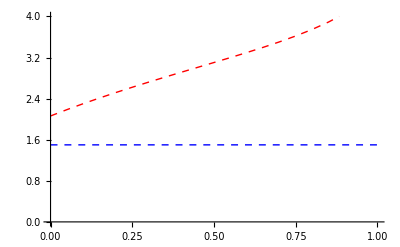

```mathematica
p1PIh=ListLinePlot[Transpose[a1PIh],PlotRange->{0,4},PlotStyle->{{Red,Dashed},{Blue,Dashed}}]
```

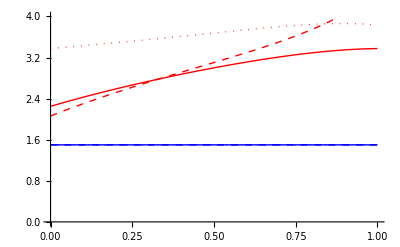

```mathematica
Show[{p1h,p1MIh,p1PIh}]
```